```mathematica
(* The Subscript[Ω, b] h^2 value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
obh2pl=0.02236;
(* The Subscript[Ω, m] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
ompl=0.3166;
(* The Subscript[H, 0] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
H0pl=3.23h0pl 10^(−18);
(* The dimensionless parameter for the Hubble constant, defined as Subscript[H, 0]/100 *)
h0pl=0.6770;

(* CMB temperature *)
Tcmb=2.7255;
(* Various constants useful for the following likelihoods *)
c=2.99792458 10^8;






(* Define Subscript[z, equality] and Subscript[a, equality] *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* H≡(Hubble(z,om,...))/(km s^-1 Mpc^-1)  We have as a starting point a flat universe with H^2=Subscript[H, 0]^2[Subscript[Ω, m,0] a^-3+Subscript[Ω, r,0] a^-4+Subscript[Ω, Λ]], then H=Subscript[H, 0] √(Subscript[Ω, m,0] a^-3(1+a^-1 Subscript[a, eq])+1-Subscript[Ω, m,0](1+Subscript[a, eq])) with Subscript[H, 0]=100 h km s^-1 Mpc^-1 and Subscript[a, eq]=Subscript[Ω, r,0]/Subscript[Ω, m,0]*) 
H[a_?NumberQ,om_?NumberQ]:=H0pl  Sqrt[a^-3 om(1+aeq[om,h0pl]/a)+(1-om(1+aeq[om,h0pl]))]
g=1/(0.529 10^-10);(*Inverse Bohr length*)
e0=1/(2(1/g)^2);
```

```mathematica
lmax[a_]:=c a NIntegrate[1/(a0^2 H[a0,ompl]),{a0,0,a}]
```

```mathematica
SolveEtilde[g_?NumericQ,L_?NumericQ]:=Module[{absEtilde,sol},(*Define the equation to solve*)equation=g Coth[(Sqrt[absEtilde] L)/Sqrt[2]]==Sqrt[2 absEtilde];
(*Find the solution numerically*)sol=FindRoot[equation,{absEtilde,e0}];(*Starting guess of 0.1*)(*Return the solution*)absEtilde/. sol]
```

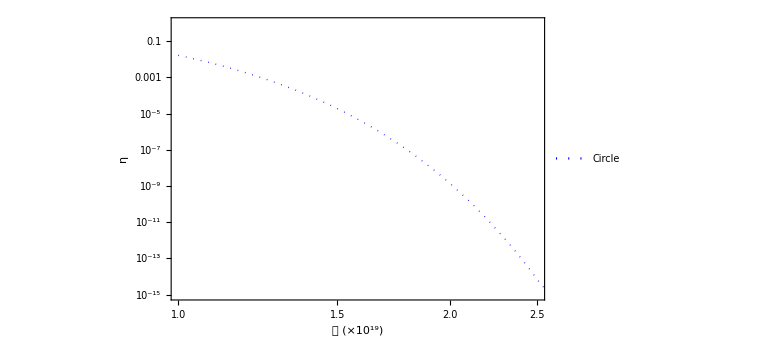

```mathematica
Plot1d=LogLogPlot[{((SolveEtilde[g,2lmax[a]]-e0)/e0)},{a, 10^-19, 10^-15},PlotRange->{{10^-19,2.5 10^-19},{10^-15,1}},PlotStyle->{{Blue,Dotted,Thick}},Frame->True,FrameLabel->{Style["𝒶 (×10^19)",28,Bold,Black,FontFamily->"Times"],(*Giant'a'*)Style["η",28,Bold,Black,FontFamily->"Times"]   (*Giant'e'*)},FrameStyle->Thick,(*Thick frame lines*)FrameTicksStyle->Directive[Black,24],(*Larger tick marks*)AxesStyle->Thick,(*Optional grid*)ImageSize->Large                 (*Ensures plot is big enough*),PlotLegends->Placed[{Style["Circle",25,Black]},{Right,Top}]      ,FrameTicks->{{Automatic,Automatic},(*Left& Right ticks:Automatic*){(*Bottom ticks:Custom positions (scaled to match a-axis)*)Table[{val 10^-19,NumberForm[val,{2,1}]},(*Tick position& label*){val,1,2.5,0.5} (*Now val is 1,1.5,2,2.5*)],None (*No top ticks*)}}]
```

```mathematica
SolveEtildeNumerical[gR_?NumericQ,L_?NumericQ,nmax_]:=Module[{absEtilde,equation},equation[absEtilde_]:=1/gR==Sqrt[2 absEtilde]-(1)/( L)*Sum[Exp[-Sqrt[nx^2+ny^2+nz^2]*Sqrt[2 absEtilde]*L]*Boole[!(nx==0&&ny==0&&nz==0)],{nx,-nmax,nmax},{ny,-nmax,nmax},{nz,-nmax,nmax}];
absEtilde/. FindRoot[equation[absEtilde],{absEtilde,1/(2*gR^2)},AccuracyGoal->22,PrecisionGoal->22]]

SolveEtildeNumericalhalfturn[gR_?NumericQ,L_?NumericQ,nmax_,nmax1_]:=Module[{absEtilde,equation},equation[absEtilde_]:=1/gR==Sqrt[2 absEtilde]+(1)/L Log[1-Exp[-2 *Sqrt[2 absEtilde]*L]]-2/L*Sum[Exp[-Sqrt[ny^2+nz^2]*Sqrt[2 absEtilde]*L],{ny,1,nmax},{nz,-2nmax1,2nmax1}]-2/L*Sum[Exp[-Sqrt[nx^2+ny^2+nz^2]*Sqrt[2 absEtilde]*L],{nx,1,nmax},{ny,-nmax,nmax},{nz,-2nmax1,2nmax1}];
absEtilde/. FindRoot[equation[absEtilde],{absEtilde,1/(2*gR^2)},AccuracyGoal->22,PrecisionGoal->22]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

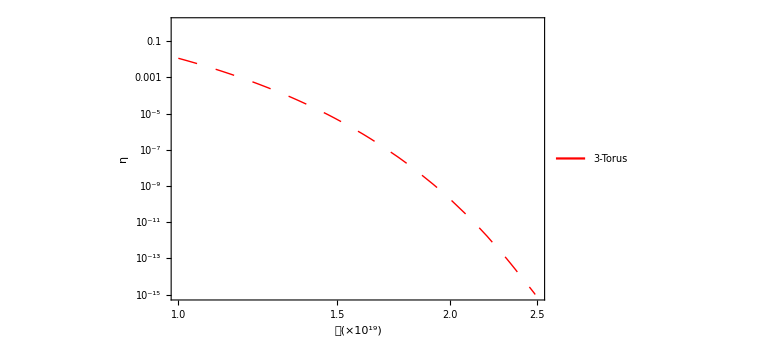

```mathematica
Plot1=LogLogPlot[{(SolveEtildeNumerical[1/g,2 lmax[a],30]-e0)/e0},{a, 10^-19, 10^-15},PlotRange->{{10^-19,2.5 10^-19},{10^-15,1}},PlotStyle->{{Red,Thick,Dashing[Large]}},Frame->True,FrameLabel->{Style["𝒶(×10^19)",28,Bold,Black,FontFamily->"Times"],(*Giant'a'*)Style["η",28,Bold,Black,FontFamily->"Times"]   (*Giant'e'*)},FrameStyle->Thick,(*Thick frame lines*)FrameTicksStyle->Directive[Black,24],(*Larger tick marks*)AxesStyle->Thick,(*Optional grid*)ImageSize->Large         ,    PlotLegends->Placed[{Style["3-Torus",25,Black]},{Right,Top}]  ,       (*Ensures plot is big enough*)FrameTicks->{{Automatic,Automatic},(*Left& Right ticks:Automatic*){(*Bottom ticks:Custom positions (scaled to match a-axis)*)Table[{val 10^-19,NumberForm[val,{2,1}]},(*Tick position& label*){val,1,2.5,0.5} (*Now val is 1,1.5,2,2.5*)],None (*No top ticks*)}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

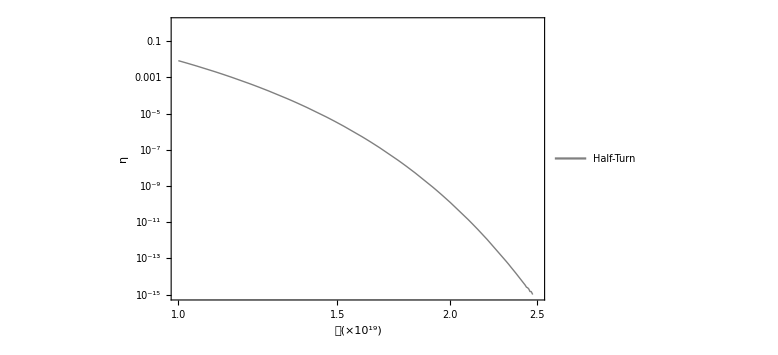

```mathematica
Plot2=LogLogPlot[{(SolveEtildeNumericalhalfturn[1/g,2 lmax[a],30,10]-e0)/e0},{a, 10^-19,10^-15},PlotRange->{{10^-19,2.5 10^-19},{10^-15,1}},PlotStyle->{{Gray,Thick},{Gray,Dashed}},Frame->True,FrameLabel->{Style["𝒶(×10^19)",28,Bold,Black,FontFamily->"Times"],(*Giant'a'*)Style["η",28,Bold,Black,FontFamily->"Times"]   (*Giant'e'*)},FrameStyle->Thick,(*Thick frame lines*)FrameTicksStyle->Directive[Black,24],(*Larger tick marks*)AxesStyle->Thick,(*Optional grid*)ImageSize->Large   ,    PlotLegends->Placed[{Style["Half-Turn",25,Black]},{Right,Top}]      ,       (*Ensures plot is big enough*)FrameTicks->{{Automatic,Automatic},(*Left& Right ticks:Automatic*){(*Bottom ticks:Custom positions (scaled to match a-axis)*)Table[{val 10^-19,NumberForm[val,{2,1}]},(*Tick position& label*){val,1,2.5,0.5} (*Now val is 1,1.5,2,2.5*)],None (*No top ticks*)}}]
```

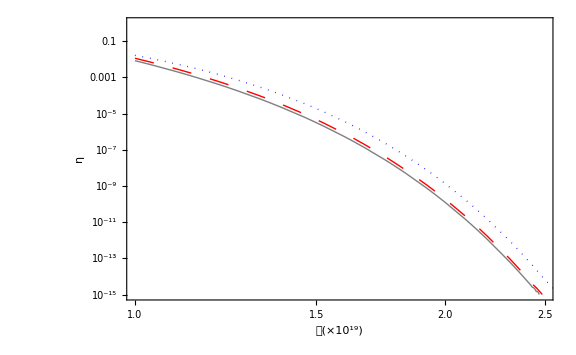

```mathematica
Show[Plot1,Plot2,Plot1d]
```